```mathematica
$Assumptions={g>0,ωs>0,Ω>0,γ>0,γb>0,L>0};
Clear[aout,aoutd,ain,aind,bout,boutd,bin,bind,a,ad,b,bd,A,Ad,h];
Qlist={aout,aoutd,ain,aind,bout,boutd,bin,bind,a,ad,b,bd,A,Ad,h};
Qlen=Length[Qlist];
Do[Evaluate[Qlist[[i]]]=i,{i,1,Qlen}];
TFlist={
{aout,ain}->1,
{aoutd,aind}->1,
{bout,bin}->1,
{boutd,bind}->1,
{aout,a}->-√(2γ),
{aoutd,ad}->-√(2γ),
{bout,b}->-√(2γb),
{boutd,bd}->-√(2γb),
{a,ain}->√(2 γ)(-ⅈ Ω)^-1,
{ad,aind}->√(2 γ)(-ⅈ Ω)^-1,
{b,bin}->√(2 γb)(-ⅈ Ω)^-1,
{bd,bind}->√(2 γb)(-ⅈ Ω)^-1,
{a,a}->-γ(-ⅈ Ω)^-1,
{ad,ad}->-γ(-ⅈ Ω)^-1,
{a,bd}->ⅈ g (-ⅈ Ω)^-1,
{ad,b}->-ⅈ g (-ⅈ Ω)^-1,
{b,b}->-γb(-ⅈ Ω)^-1,
{bd,bd}->-γb(-ⅈ Ω)^-1,
{b,ad}->ⅈ g (-ⅈ Ω)^-1,
{bd,a}->-ⅈ g (-ⅈ Ω)^-1,
{a,A}->-ωs(-ⅈ Ω)^-1,
{ad,Ad}->-ωs(-ⅈ Ω)^-1,
{A,a}->ωs(-ⅈ Ω)^-1,
{Ad,ad}->ωs(-ⅈ Ω)^-1,
{A,h}->ⅈ G L (-ⅈ Ω)^-1,
{Ad,h}->-ⅈ G L (-ⅈ Ω)^-1
};
DM=SparseArray[TFlist,{Qlen,Qlen}](*Dynamical matrix*);
IMN=SparseArray[{Band[{1,1}]->1},{Qlen,Qlen}];
TFM=Inverse[IMN-DM](*Transfer function matrix*);
```

```mathematica
umat=1/(√2){{1,1},{-ⅈ,ⅈ}};
umat2={{umat,0},{0,umat}}//ArrayFlatten;
inputOutput={{TFM[[aout,ain]],TFM[[aout,aind]],TFM[[aout,bin]],TFM[[aout,bind]]},
{TFM[[aoutd,ain]],TFM[[aoutd,aind]],TFM[[aoutd,bin]],TFM[[aoutd,bind]]},
{TFM[[bout,ain]],TFM[[bout,aind]],TFM[[bout,bin]],TFM[[bout,bind]]},
{TFM[[boutd,ain]],TFM[[boutd,aind]],TFM[[boutd,bin]],TFM[[boutd,bind]]}}//Simplify
strain={TFM[[aout,h]],TFM[[aoutd,h]],TFM[[bout,h]],TFM[[boutd,h]]}//Simplify
```

{{(g^2 Ω+(ⅈ γb+Ω) (-ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0,0,(2 ⅈ g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))},{0,(g^2 Ω+(ⅈ γb+Ω) (-ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),-(2 ⅈ g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0},{0,(2 ⅈ g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),(g^2 Ω+(-ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0},{-(2 ⅈ g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0,0,(g^2 Ω+(-ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))}}

{(√2 G L √γ (γb-ⅈ Ω) ωs)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),-(√2 G L √γ (γb-ⅈ Ω) ωs)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),-(ⅈ √2 g G L √γb ωs)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),-(ⅈ √2 g G L √γb ωs)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))}

```mathematica
inputOutputQ=umat2.inputOutput.Inverse[umat2]//Simplify
strainQ=umat2.strain//Simplify
readout={0,k1,k2,0};
```

{{(g^2 Ω+(ⅈ γb+Ω) (-ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0,0,(2 g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))},{0,(g^2 Ω+(ⅈ γb+Ω) (-ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),(2 g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0},{0,(2 g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),(g^2 Ω+(-ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0},{(2 g √(γ γb) Ω)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0,0,(g^2 Ω+(-ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2))}}

{0,-(2 ⅈ G L √γ (γb-ⅈ Ω) ωs)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),-(2 ⅈ g G L √γb ωs)/(g^2 Ω+(ⅈ γb+Ω) (ⅈ γ Ω+Ω^2-ωs^2)),0}

```mathematica
(*Abs[(readout.inputOutputQ.Transpose[inputOutputQ].Transpose[{readout}])/(strainQ.readout)]^2//ComplexExpand//Simplify*)
```

```mathematica
(Abs[strainQ.readout]^2//ComplexExpand//Simplify)/.γb->0/.k1->1//Simplify
```

(4 G^2 L^2 γ ωs^2)/(g^4+γ^2 Ω^2+2 g^2 (Ω^2-ωs^2)+(Ω^2-ωs^2)^2)

```mathematica
(* recovered transmission readout *) (4 G^2 L^2 γ ωs^2)/(γ^2 Ω^2+(g^2-ωs^2+Ω^2)^2);
```

```mathematica
shh=((readout.inputOutputQ.ConjugateTranspose[inputOutputQ].Transpose[{readout}])[[1]]/Abs[strainQ.readout]^2)//ComplexExpand//Simplify
```

(g^4 (k1^2+k2^2) Ω^2+8 g^3 k1 k2 √(γ γb) Ω^2+8 g k1 k2 √(γ γb) Ω^2 (γ γb+Ω^2-ωs^2)+2 g^2 (k1^2+k2^2) Ω^2 (3 γ γb+Ω^2-ωs^2)+(k1^2+k2^2) (γb^2+Ω^2) (γ^2 Ω^2+(Ω^2-ωs^2)^2))/(4 G^2 L^2 (g^2 k2^2 γb+2 g k1 k2 γb √(γ γb)+k1^2 γ (γb^2+Ω^2)) ωs^2)

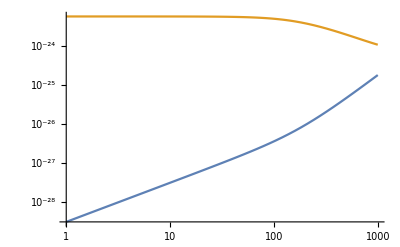

```mathematica
LogLogPlot[Evaluate[{√(1/((4 G^2 L^2 γ ωs^2)/(γ^2 Ω^2+(g^2-ωs^2+Ω^2)^2))),√shh/.γb->γ/.k1->1/.k2->0}/.g->ωs/.{G->ps[Subscript[G, 0]],L->40000,γ->ps[Subscript[γ, f]],ωs->ps[Subscript[ω, SP]],g->ps[g]}/.Ω->2 π f],{f,1,1000}]
```

```mathematica
Solve[((Abs[strainQ.readout]^2//ComplexExpand//Simplify)/.γb->γ/.k2->√(1-k1^2))==(4 G^2 L^2 γ ωs^2)/(g^4+γ^2 Ω^2+(g^2-ωs^2+Ω^2)^2),k1]
```

$Aborted

```mathematica
k1sol=(k1/.Solve[(((1/shh//ComplexExpand//Simplify)/.γb->γ/.k2->√(1-k1^2))==(4 G^2 L^2 γ ωs^2)/(g^4+γ^2 Ω^2+(g^2-ωs^2+Ω^2)^2))/.{G->ps[Subscript[G, 0]],L->40000,γ->ps[Subscript[γ, f]],ωs->ps[Subscript[ω, SP]],g->ps[g]},k1])[[1]]
```

$Aborted

```mathematica
(Abs[strainQ.readout]^2//ComplexExpand//Simplify)/.k2->√(1-k1^2)
```

(4 G^2 L^2 (g^2 (1-k1^2) γb+2 g k1 √(1-k1^2) γb √(γ γb)+k1^2 γ (γb^2+Ω^2)) ωs^2)/(g^4 Ω^2-2 g^2 Ω^2 (γ γb-Ω^2+ωs^2)+(γb^2+Ω^2) (γ^2 Ω^2+(Ω^2-ωs^2)^2))

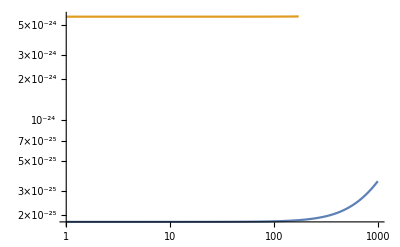

```mathematica
LogLogPlot[Evaluate[{√(1/((4 G^2 L^2 γ ωs^2)/(γ^2 Ω^2+(g^2-ωs^2+Ω^2)^2))),√shh/.γb->γ/.k1->k1sol/.k2->√(1-k1sol^2)}/.{G->ps[Subscript[G, 0]],L->40000,γ->ps[Subscript[γ, f]],ωs->ps[Subscript[ω, SP]],g->ps[g]}/.Ω->2 π f],{f,1,1000}]
```